# Potential Testing for Claire

This notebook shows an example of how to load in HDF5 potential data from chplUltra and what it looks like.

```mathematica
SetDirectory[NotebookDirectory[] ];
```

### How does importing the potential work?

Below, ff opens the file “phi_ 000000.h5”, while ff[“/phi”] gets the data under the “/phi” key--aka, the 128 x 128 x 128 array of potential values.

```mathematica
ff = Import["test/saves/phi_000000.h5", "Data"];
pot = ff["/phi"] (* this is the actual data you want!*)
```

{1}
 |  |  |  |

Below, we can plot it quickly (ArrayPlot[] is not very pretty but it’s quite quick; DensityPlot[] is the version with more bells and whistles). This plots the y-z plane for the 64th x-index of pot:

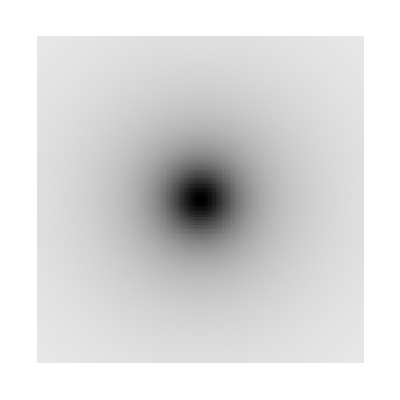

```mathematica
ArrayPlot[pot[[64,;;,;;]]]
```

We can also plot one cross section of potential as below:

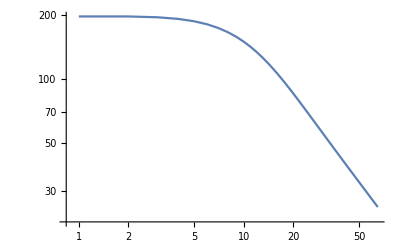

```mathematica
ListLogLogPlot[Abs@pot[[64,64,64;;]], Joined->True]
```

Note that above you’re just plotting the values of pot against numbers running from 1 to 64. If you wanted to define a radius to plot against, you could do something like this:

```mathematica
rval = (Range[0,64] +0.5)* 2.0/128;
```

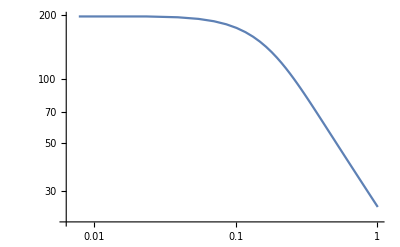

```mathematica
ListLogLogPlot[Transpose[{rval,Abs@pot[[64,64,64;;]]}], Joined->True]
```

### What is the run.h5 file?

The run.h5 file is sort of the main output of chplUltra--it has things like the evolution of the mass, the density and energy profiles, etc.

```mathematica
ff = Import["test/run.h5", "Data"];
Keys@ff
```

{/info,/profiles/000000/KEc,/profiles/000000/KEq,/profiles/000000/PE,/profiles/000000/counts,/profiles/000000/mass,/profiles/000001/KEc,/profiles/000001/KEq,/profiles/000001/PE,/profiles/000001/counts,/profiles/000001/mass,/profiles/000002/KEc,/profiles/000002/KEq,/profiles/000002/PE,/profiles/000002/counts,/profiles/000002/mass,/profiles/000003/KEc,/profiles/000003/KEq,/profiles/000003/PE,/profiles/000003/counts,/profiles/000003/mass,/profiles/000004/KEc,/profiles/000004/KEq,/profiles/000004/PE,/profiles/000004/counts,/profiles/000004/mass,/profiles/000005/KEc,/profiles/000005/KEq,/profiles/000005/PE,/profiles/000005/counts,/profiles/000005/mass,/profiles/000006/KEc,/profiles/000006/KEq,/profiles/000006/PE,/profiles/000006/counts,/profiles/000006/mass,/profiles/000007/KEc,/profiles/000007/KEq,/profiles/000007/PE,/profiles/000007/counts,/profiles/000007/mass,/profiles/000008/KEc,/profiles/000008/KEq,/profiles/000008/PE,/profiles/000008/counts,/profiles/000008/mass,/profiles/000009/KEc,/profiles/000009/KEq,/profiles/000009/PE,/profiles/000009/counts,/profiles/000009/mass,/profiles/000010/KEc,/profiles/000010/KEq,/profiles/000010/PE,/profiles/000010/counts,/profiles/000010/mass,/timing}

"Keys" are what you give ff to ask for a specific bit of information. Eg, if you wanted to know how much time each of the steps took:

```mathematica
ff["/timing"]
```

{<|kick→0.,stream→0.,pot→0.,sponge→0.,analyse→0.|>,<|kick→0.021387,stream→0.353974,pot→0.708924,sponge→0.000174,analyse→0.810269|>,<|kick→0.04251,stream→0.70321,pot→1.41164,sponge→0.000348,analyse→1.29956|>,<|kick→0.063384,stream→1.05192,pot→2.11392,sponge→0.000521,analyse→1.7646|>,<|kick→0.08438,stream→1.40097,pot→2.81625,sponge→0.00069,analyse→2.28825|>,<|kick→0.105227,stream→1.74935,pot→3.5149,sponge→0.000862,analyse→2.76687|>,<|kick→0.126181,stream→2.09756,pot→4.21805,sponge→0.001035,analyse→3.26068|>,<|kick→0.146845,stream→2.44703,pot→4.91535,sponge→0.001208,analyse→3.77778|>,<|kick→0.167488,stream→2.79581,pot→5.61542,sponge→0.001385,analyse→4.26319|>,<|kick→0.188095,stream→3.14471,pot→6.31933,sponge→0.001556,analyse→4.7534|>,<|kick→0.208651,stream→3.49287,pot→7.01879,sponge→0.001728,analyse→5.2262|>}

See an example of how to get to the DM density profiles from run.h5 below :

```mathematica
ff = Import["test/run.h5", "Data"];
rho = ff["/profiles/000000/mass"]/ff["/profiles/000000/counts"];
```

You have to remember to divide by counts, otherwise you’ll get a cumulative density instead of a density profile!

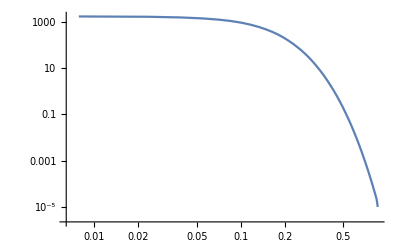

```mathematica
rval = (Range[1,64] -0.5)* 2.0/128;
ListLogLogPlot[Transpose[{rval,rho}], Joined->True]
```

### chplUltra Units

λ and m22 are constants; we tend to set them to 1.

#### Code units and conversions

```mathematica
maxion[m22_]:= (m22 10^-22)*(1.783*10^-36)  (* kg *)
hbar=1.0545718*10^-34; (* m^2 kg/s *)
parsec=3.0857*10^16 ; (* m *)
ly=9.4607*10^15 ; (* m *)
kpc = 3.086*10^19; (* m *)
mSun=1.989* 10^30; (* kg *)
G=6.673*10^-11; (*N m2 kg-2.*)
omegaM0=0.31 ;
H0=(67.7 * 10^3)/(parsec*10^6) ; (* s^-1 *)
```

#### Defining code units (in SI):

```mathematica
timeUnit[ λ_]:=((8*Pi)/(3 * H0^2* omegaM0))^(1/2)λ^-2 (*seconds*)
lengthUnit[m22_, λ_] := ((8 π hbar^2)/(3*maxion[m22]^2* H0^2*omegaM0))^(1/4)λ^-1 (*meters*)
massUnit[m22_, λ_] := 1/G((8 Pi)/(3 * H0^2*omegaM0))^(-1/4)(hbar/maxion[m22])^(3/2)λ^1 (*kg*)
```

#### Code units in “astronomical” units:

```mathematica
timeUnityears[ λ_] := timeUnit[ λ]/(Pi * 10^7) (* years *)
lengthUnitkpc[m22_, λ_] := lengthUnit[m22, λ]/kpc (* kpc *)
massUnitsolar[m22_, λ_] := massUnit[m22, λ]/mSun (* Solar masses *)
```

```mathematica
lengthUnitkpc[1,1]
```

38.3609

```mathematica
lengthUnitkpc[1,2.55739]
```

15.

```mathematica
Clear[λ]
```

```mathematica
Solve[((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)λ^-1/kpc ==15, λ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{λ→2.55739}}

Need to calculate the lambda you want for a choice of parameters; in the meantime, posting the table below with some ideas:

-Graphics-

### Units

λ = 8.7 is equivalent to one gigayear in code units
1. timeUnit[8.7] converts a gigayear from code units to seconds
2. timeUnityears[8.7] converts a gigayear from code units to years
3.

```mathematica
timeUnit[1]
timeUnityears[1]
lengthUnit[1,1]
lengthUnitkpc[1,1]
((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)
```

2.36943×10^18

7.54212×10^10

1.18382×10^21

38.3609

1.18382×10^21

### Run in ChplUltra units

#### 1. Dimensionless ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp1pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10,6;;7}];
bp1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",10;;20,6;;7}];
bp1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",100;;110,6;;7}];
bp1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",200;;210,6;;7}];
bp1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",300;;310,6;;7}];
bp1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",990;;1000,6;;7}];
bp1pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1990;;2000,6;;7}];
bp1pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",2990;;3000,6;;7}];
bp1pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",3990;;4000,6;;7}];
bp1pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",4990;;5000,6;;7}];
bp1pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",5990;;6000,6;;7}];
bp1pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",6990;;7000,6;;7}];
bp1pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",7990;;8000,6;;7}];
bp1pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",8990;;9000,6;;7}];
bp1pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

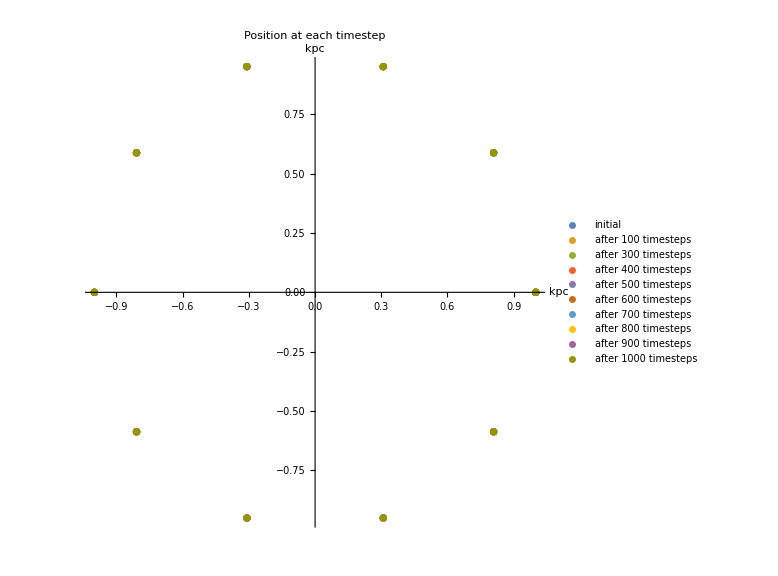

```mathematica
bp1posgraph = ListPlot[{bp1pos1,bp1pos100,bp1pos300,bp1pos400,bp1pos500,bp1pos600,bp1pos700,bp1pos800,bp1pos900,bp1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 2. ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1;;10,6;;7}];
bp2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",10;;20,6;;7}];
bp2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",100;;110,6;;7}];
bp2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",200;;210,6;;7}];
bp2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",300;;310,6;;7}];
bp2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",990;;1000,6;;7}];
bp2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1990;;2000,6;;7}];
bp2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",2990;;3000,6;;7}];
bp2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",3990;;4000,6;;7}];
bp2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",4990;;5000,6;;7}];
bp2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",5990;;6000,6;;7}];
bp2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",6990;;7000,6;;7}];
bp2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",7990;;8000,6;;7}];
bp2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",8990;;9000,6;;7}];
bp2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

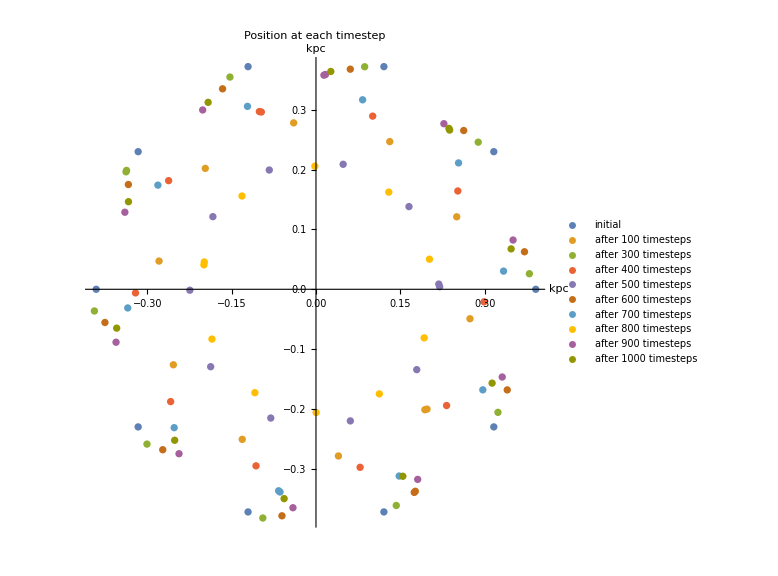

```mathematica
bp2posgraph = ListPlot[{bp2pos1,bp2pos100,bp2pos300,bp2pos400,bp2pos500,bp2pos600,bp2pos700,bp2pos800,bp2pos900,bp2pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```